```mathematica
$MinPrecision=53;
```

### Defining The Domains

#### u Domain(s)

```mathematica
prec=64;
```

```mathematica
uOuterMin=1/10;
uOuterMax= 9/10;
uOuterDomains=1;
uOuterNodes=48;
uInnerNodes=12;
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];
```

```mathematica
InterfaceNodes
```

{1/10,9/10}

```mathematica
GetuDomain[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Flatten[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,2,uOutNodes}],{j,2,IntfaceNodes//Length}],1],prec];
Join[uInner,uOut]
]
```

```mathematica
uValues=GetuDomain[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];
```

```mathematica
uValues[[13]]//Precision
```

64.

#### x Domain

```mathematica
xMin=-5;
xMax=5;
xNodes=12;
Deltax=Abs[xMin-xMax]/xNodes;
xValues=Table[xMin+i Deltax,{i,0,xNodes}];
```

#### y Domain

```mathematica
yMin=-5;
yMax=5;
yNodes=12;
Deltay=Abs[yMin-yMax]/yNodes;
yValues=Table[yMin+i Deltay,{i,0,yNodes}];
```

#### Grid

```mathematica
MyGrid=Table[{uValues[[u]],xValues[[x]],yValues[[y]]},{u,1,uValues//Length},{x,1,xValues//Length},{y,1,yValues//Length}];
```

## Boosted Black Brain

## Constant boosting

#### ρ

```mathematica
ClearAll[u1]
```

```mathematica
u0d=-2^(1/2);
(*u1[x_,y_]:=Cos[q x];*)
u1=1;
u2=0;
q=(20 Pi)/(xMax-xMin);
b=1;
```

```mathematica
ClearAll[u]
```

```mathematica
ϵ=10^-20;
```

```mathematica
(*uofρ=NDSolve[{D[u[ρ],ρ]==(u[ρ]^2/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2)),u[ϵ]==ϵ},u,{ρ,ϵ,1}][[1,1]];*)
```

```mathematica
ρofu=DSolve[{D[ρ[u],u]==(u^2/ρ[u]^2(1+(b ρ[u])^3(u1^2+u2^2))^(-1/2))^-1},ρ,{u,0,1}][[1,1]];
```

Q: Boundary conditions: at ρ=0 or =1?
A: At 0
Q: Do we know where is the horizon in the u domain?
A: Yes at u(ρ=1).

Here I compute r in function of rho. I set no boundary conditions for the ODE but I then impose the constant of integration to be zero

```mathematica
rofρ=DSolve[{D[r[ρ],ρ]==(-1/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2))(*,r[1]==1*)},r,ρ][[1,1]];
r/.rofρ
```

Function[{ρ},C[1]+Hypergeometric2F1[-1/3,1/2,2/3,-ρ^3]/ρ]

```mathematica
(r/.rofρ)[1]
```

C[1]+Hypergeometric2F1[-1/3,1/2,2/3,-1]

```mathematica
rofρ=(r/.rofρ)/.C[1]->0
```

Function[{ρ},0+Hypergeometric2F1[-1/3,1/2,2/3,-ρ^3]/ρ]

```mathematica
InverseFunction[rofρ][1]
```

Root1.50Root[{-1+Hypergeometric2F1[-1/3,1/2,2/3,-#1^3]/#1&,1.49504832898603048466494223738}]1.4950483289860306

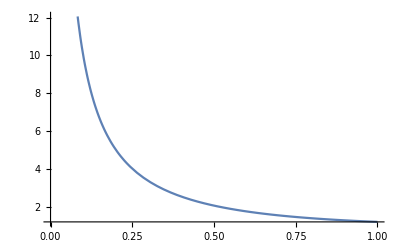

```mathematica
Plot[rofρ[ρ],{ρ,0,1}]
```

```mathematica
N[rofρ[1]^-1,64]
```

0.8338097372270937048098805420823810844855493351334153302676245139

#### a3

Here I compute the initial data for a3. In the limit at infinity, ρ goes to zero, as u. Anyway, they don’t have the same asymptotic behaviour so we need to take the expansion of A, substitute u to its expression that depends on  ρ, and expand in terms of ρ around infinity (where ρ=0). In this way we have an expression of our variable in terms of ρ at infinity that has to match the expression for A in the Turbulence draft (Eq. 3.7).

```mathematica
AExp=1/u^2+u a3[t,u,z,y]+(2 ξ[t,z,y])/u+ξ[t,z,y]^2-2 Derivative[1,0,0][ξ][t,z,y];
```

```mathematica
AExpOfρ=AExp/.u->rofρ[ρ]^-1(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,1}]&
```

1/ρ^2+(2 ξ[t,z,y])/ρ+(ξ[t,z,y]^2-2 ξ^(1,0,0)[t,z,y])+(1/2+a3[t,0,z,y]) ρ+O[ρ]^2

```mathematica
AExpOfρ//Normal//Simplify
```

1/ρ^2+ρ (1/2+a3[t,0,z,y])+(2 ξ[t,z,y])/ρ+ξ[t,z,y]^2-2 ξ^(1,0,0)[t,z,y]

Let’s look for ξ

```mathematica
ξRule=Solve[2-2 Hypergeometric2F1[-1/3,1/2,2/3,-1]+2 ξ[t,z,y]==0, ξ[t,z,y]]
```

{{ξ[t,z,y]→-1+Hypergeometric2F1[-1/3,1/2,2/3,-1]}}

```mathematica
(-1+Hypergeometric2F1[-1/3,1/2,2/3,-1])^2-2 (-1+Hypergeometric2F1[-1/3,1/2,2/3,-1]) ξ[t,z,y]+ξ[t,z,y]^2/.ξRule
```

{0}

Ok

```mathematica
-1+Hypergeometric2F1[-1/3,1/2,2/3,-1]//N//FullForm
```

0.199314

```mathematica
AToMatch=ρ^-2(1-(b ρ)^3(1+u1^2+u2^2))//Simplify
```

1/ρ^2-2 ρ

```mathematica
AExpOfρ//Normal//Simplify
```

1/ρ^2+ρ (1/2+a3[t,0,z,y])+(2 ξ[t,z,y])/ρ+ξ[t,z,y]^2-2 ξ^(1,0,0)[t,z,y]

```mathematica
rofρ[1]
```

1

I compare the same order coefficient of ρ

```mathematica
a3[t,0,z,y]/.Solve[Coefficient[AToMatch,ρ]==Coefficient[AExpOfρ,ρ],a3[t,0,z,y]]//Flatten
```

{-5/2}

As in the turbulence draft.

#### f1 (and f2)

Same procedure as above but for F1.

```mathematica
FExp=u f1[t,z,y];
```

```mathematica
u/.u->rofρ[ρ]^-1
```

ρ/Hypergeometric2F1[-1/3,1/2,2/3,-ρ^3]

```mathematica
FExpOfρ=FExp/.u->rofρ[ρ]^-1(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,1}]&
```

f1[t,z,y] ρ+O[ρ]^2

```mathematica
FToMatch=(b ρ)^3/ρ^2 u0 u1
```

-√2 ρ

```mathematica
(*f1[t,z,y]/.*)Solve[Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ],f1[t,z,y]]//Flatten
```

{f1[t,z,y]→-√2}

Matching with the turbulence draft.

#### ξ (VEV of S)

1/u+u^2 Sfin[t,u,z,y]+ξ[t,z,y]

```mathematica
SExp=1/u+ξ[t,z,y]+u^2 s0[t,u,z,y];
```

```mathematica
SExpOfρ=SExp/.u->rofρ[ρ]^-1/.ξRule[[1]]//Series[#,{ρ,0,2}]&
```

1/ρ+(1/4+s0[t,0,z,y]) ρ^2+O[ρ]^3

```mathematica
SToMatch=((1/ρ^2 √(1+ρ^3))^(1/2)//Series[#,{ρ,0,2}]&)/.√(1/ρ^2)->1/ρ//Simplify
```

1/ρ+ρ^2/4+O[ρ]^3

```mathematica
s0[t,0,z,y]/.Solve[Coefficient[SToMatch,ρ^2]==Coefficient[SExpOfρ,ρ^2],s0[t,0,z,y]]//Flatten
```

{0}

Matching the turbulence draft.

#### B Function

The initial data for B is different, since B is defined through the entire domain. We need to invert the function r(ρ). This is a problem, since that is not invertible analytically.

The min value of u is:

```mathematica
uOfρAtInf=1/rofρ[ϵ]//N[#,64]&
```

9.9999999999999999999999999999999999999999999999999999999999975×10^-21

The  horizon is at

```mathematica
uh=rofρ[1]^-1//N[#,$MinPrecision]&
```

0.83380973722709370480988054208238108448554933513341533

```mathematica
Numericaluofρ=u/.DSolve[{D[u[ρ],ρ]==(u[ρ]^2/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2)),u[ϵ]==ϵ},u,{ρ,0,1}][[1,1]];
```

```mathematica
Numericaluofρ[2]//Precision
```

∞

```mathematica
Nρofu[u_]:=InverseFunction[Numericaluofρ][u];
```

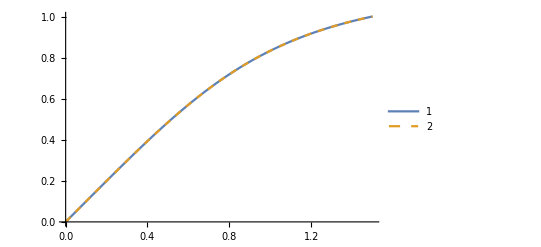

```mathematica
Show[Plot[{Numericaluofρ[ρ],rofρ[ρ]^-1},{ρ,0,1.5},PlotStyle->{Thick,Dashed},PlotLegends->Automatic,PlotRange->All]]
```

```mathematica
Numericaluofρ[0.1]//Precision
```

MachinePrecision

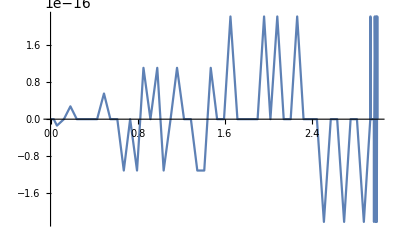

```mathematica
Plot[N[(Numericaluofρ[N[ρ,25]]-rofρ[N[ρ,25]]^-1),32],{ρ,0,uOuterDomains}]
```

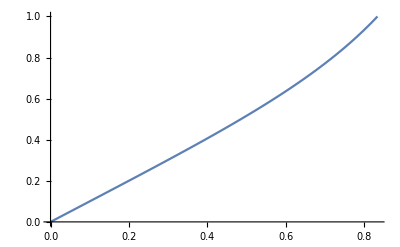

```mathematica
Plot[{InverseFunction[Numericaluofρ][u]},{u,Numericaluofρ[0],Numericaluofρ[1]}]
```

```mathematica
ρofuValues=(InverseFunction[Numericaluofρ])/@uValues;
```

```mathematica
ρofuValues[[3]]//Precision
```

64.

```mathematica
ρofr=InverseFunction[rofρ];
```

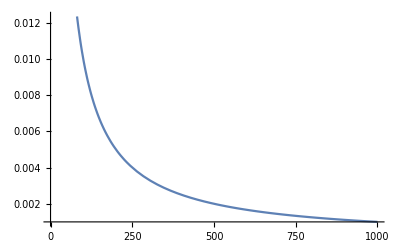

```mathematica
Plot[ρofr[r],{r,0.0001,1000}]
```

```mathematica
(*NDSolve[{D[SS[r],{r,2}]+SS[r]/4 D[-1/2Log[(1+(b ρofr[r])^3 u1^2)/(1+(b ρofr[r])^3 u2^2)],r]==0,SS[]},SS,r]*)
```

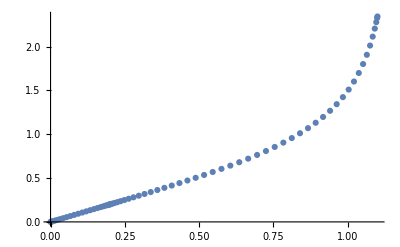

```mathematica
ListPlot[Transpose[{uValues,ρofuValues}]]
```

```mathematica
Log[1+ρofuValues[[-1]]]//N
```

1.2073

```mathematica
InverseFunction[Numericaluofρ]
```

InverseFunction[Function[{ρ},-(ρ/(100000000000000000000 ρ (-1+Hypergeometric2F1[-1/3,1/2,2/3,-1/1000000000000000000000000000000000000000000000000000000000000])-Hypergeometric2F1[-1/3,1/2,2/3,-ρ^3]))]]

```mathematica
InverseFunction[Numericaluofρ][0.1]
```

0.100025

```mathematica
Series[-1/2 Log[(1+(b InverseFunction[Numericaluofρ][u])^3 u1^2)/(1+(b InverseFunction[Numericaluofρ][u])^3 u2^2)],{u,0,1}]//N
```

```mathematica
-0.5 Log[1.+(InverseFunction[Function[{ρ},-(ρ/(100000000000000000000 ρ (-1+Hypergeometric2F1[-1/3,1/2,2/3,-1/1000000000000000000000000000000000000000000000000000000000000])-Hypergeometric2F1[-1/3,1/2,2/3,-ρ^3]))]][0])^3]//N
```

0.

```mathematica
InitialB=-1/2 Log[(1+(b ρofuValues)^3 u1^2)/(1+(b ρofuValues)^3 u2^2)] uValues^-3;
```

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
MachinePrecision//N
```

15.9546

```mathematica
"0005237856364186788"//StringLength
```

19

```mathematica
InitialB[[13]]
```

-0.000523785636418678850975434712444361577212064819515044454291039165

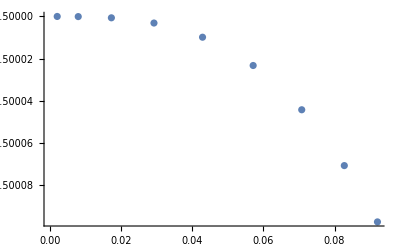

```mathematica
ListPlot[Transpose[{uValues,InitialB}][[;;10]],PlotRange->All]
```

```mathematica
InitialB[[1]]=-0.5
```

-0.5

```mathematica
ExportData=Join[{InitialB[[;;uInnerNodes]]},Table[InitialB[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1)]],{i,0,uOuterDomains-1}]];
```

```mathematica
ExportDataStr=Map[ToString,ExportData,{2}];
```

```mathematica
(Map[ToString,ExportData,{2}])[[1,2]]
```

-9
4.15404413895774069980019735045623554014062551747702550477813985 10

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->ExportData[[i]],{i,1,ExportAttributes//Length}];
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BBB.h5

```mathematica
(*Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB.h5"]*)
```

Import::nffil: File /home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB.h5 not found during Import.

$Failed

```mathematica
rofρ[1]^-1//N
```

0.83381

```mathematica
ξ[t,z,y]/.ξRule[[1,1]]//N//FullForm//Print
```

0.199314

From Jecco

```mathematica
BJecco={0.,-4.1540441389577405*^-9,-2.500300908963684*^-7,-2.5695891453335936*^-6,-0.000012486068183858487,-0.00003943413060273409,-0.00009316605426870659,-0.0001772433293798708,-0.0002832865060861823,-0.0003902164153413663,-0.0004703414869800297,-5.001250541924607*^-7,-5.485590945575364*^-7,-7.167495814621999*^-7,-1.0862768461626769*^-6,-1.8417833206355192*^-6,-3.363723998512157*^-6,-6.396414444440832*^-6,-0.000012321680054236695,-0.000023555325109773874,-0.00004404274620410723,-0.00007975623863915222,-0.00013900121012125244,-0.00023225590525186122,-0.000371252324275859,-0.0005671075572358106,-0.000827557816298585,-0.0011536977142639693,-0.0015369836907464353,-0.0019574763284838552,-0.0023842318353721626,-0.0027783424598468395,-0.0030984304218701917,-0.0033076161162341237,-0.003380384740113918,-0.00345449443945899,-0.0036836014880946553,-0.004088501857099664,-0.004705331709318862,-0.005587538150634913,-0.006808088548816569,-0.008461243567947231,-0.010662903434809384,-0.013548228977439897,-0.017265045923792462,-0.021961610695061487,-0.02776780821085592,-0.03476988782453115,-0.04298043755640154,-0.05230729093894036,-0.06252707654595896,-0.0732705617587446,-0.08402708016108967,-0.09417349640179347,-0.10302904762332081,-0.10993141497777362,-0.11432286865610522,-0.11583042527839134,-0.11735567374165116,-0.1220099168986365,-0.1300306857770196,-0.14182021869242173,-0.15795342497748113,-0.17918580875059767,-0.2064579503475033,-0.24089200996032162,-0.28377459091172824,-0.3365192514693503,-0.40060100419435546,-0.4774541763491072,-0.5683236975071804,-0.6740576922208321,-0.7948257035259455,-0.9297425429627514,-1.0763771206025035,-1.2301433748824764,-1.383641950398675,-1.52620514063904,-1.6442188617607132,-1.7230419239413868,-1.7508532346410501};
```

```mathematica
InitialB[[-1]]
```

```mathematica
BJecco[[-1]]
```

-1.75085

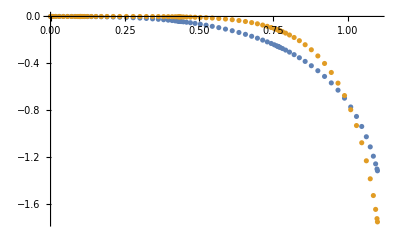

```mathematica
ListPlot[{Transpose[{uValues,InitialB}],Transpose[{uValues,BJecco}]},PlotRange->All]
```

### A function (for check)

#### A From Jecco

```mathematica
AJecco={-2.5,-2.500000004465527,-2.500000268782439,-2.5000027623109555,-2.5000134225856705,-2.500042392312419,-2.500100156980378,-2.500190549145636,-2.500304565096476,-2.5004195435590906,-2.5005057055958093,99.74994622655059,96.7122024669462,88.43187434940121,76.93542422354069,64.45017739493609,52.6402393099266,42.38757534163951,33.951100680417504,27.22831625744488,21.964354284370263,17.874886283486155,14.702896085112773,12.237184517233036,10.312686408589446,8.803903668325031,7.616862452729753,6.681784069613328,5.94712389377118,5.37498955593758,4.937730668253434,4.615454909884928,4.394255783818254,4.264985734960386,4.2224560544630005,4.18033311306929,4.057105802735426,3.861646748187931,3.6070729691513685,3.3087543257271816,2.982324618458698,2.6420964716614614,2.3000762714717293,1.9655759953163905,1.6452904366470416,1.3436635732197602,1.0633837960765615,0.8058919743412939,0.5718336345133503,0.36142372980503795,0.17471619375754718,0.011782811426974526,-0.127189014857127,-0.2418682313353343,-0.33180887285977206,-0.3965197305420878,-0.4355551627115424,-0.4486041625262347,-0.46163190758447453,-0.5003516679176622,-0.5637198109716819,-0.6501437605624925,-0.757672949220536,-0.8842165760410374,-1.0277556251420068,-1.186523902725671,-1.359143249191712,-1.5447076278835181,-1.7428163121030578,-1.9535560504513279,-2.1774244402273144,-2.415170118147356,-2.6674968885768964,-2.934535920766238,-3.214936620079632,-3.504394949974637,-3.793536729379919,-4.065547820476541,-4.295068777842759,-4.451228148921696,-4.506950755180788};
```

#### Analytic expression for A

```mathematica
A[u_]:=1/Nρofu[u]^2(1-b^3 Nρofu[u]^3(1+u1^2+u2^2));
Afin[u_]:=(-1/u^3+1/(u Nρofu[u]^2)(1-2 Nρofu[u]^3));
```

```mathematica
(A/@uValues)[[2]]
```

Power::infy: Infinite expression 1/0 encountered.

243780.664536102072948517054739809672724530907193429439060241634

```mathematica
uValues[[3]]//Precision
```

64.

#### Outer Nodes

```mathematica
uValues[[uInnerNodes+1]]//N
```

0.101552

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-1]],(A/@uValues[[uInnerNodes+1;;-1]])}],Transpose[{uValues[[uInnerNodes+1;;-1]],AJecco[[uInnerNodes+1;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.015] ,PointSize[0.0075]},ImageSize->Large,PlotLabel->A Function Comparison]
```

-Graphics-

```mathematica
FinalP=-1;
```

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;FinalP]],(A/@uValues[[uInnerNodes+1;;FinalP]])-AJecco[[uInnerNodes+1;;FinalP]]}]},PlotRange->All,PlotLabels->{"Error"},ImageSize->Large,PlotLabel->Absolute Error]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;FinalP]],((A/@uValues[[uInnerNodes+1;;FinalP]])-AJecco[[uInnerNodes+1;;FinalP]])/(A/@uValues[[uInnerNodes+1;;FinalP]])}]},PlotRange->All,PlotLabels->{"Error"},ImageSize->Large,PlotLabel->Relative Error]
```

-Graphics-

#### Inner Nodes

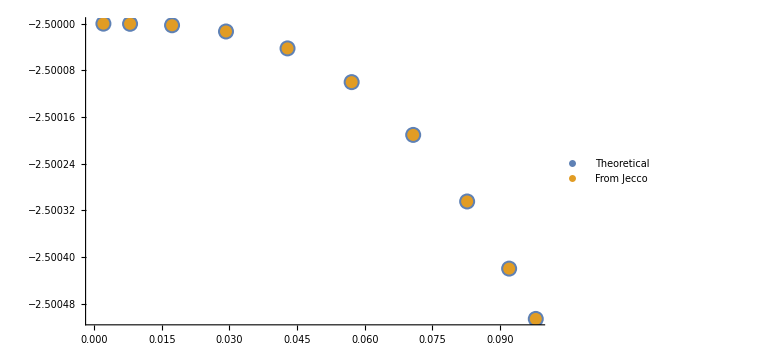

```mathematica
ListPlot[{Transpose[{uValues[[2;;uInnerNodes-1]],(Afin/@uValues[[2;;uInnerNodes-1]])}],Transpose[{uValues[[2;;uInnerNodes-1]],AJecco[[2;;uInnerNodes-1]]}]},PlotRange->All,PlotLegends->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

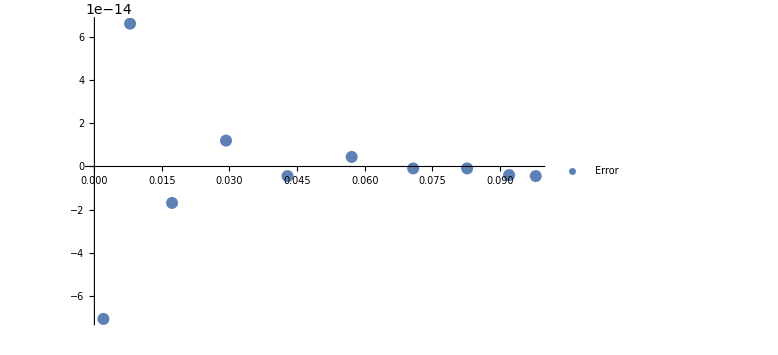

```mathematica
ListPlot[Transpose[{uValues[[2;;uInnerNodes-1]],(Afin/@uValues[[2;;uInnerNodes-1]])-AJecco[[2;;uInnerNodes-1]]}],PlotRange->All,PlotLegends->{"Error"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

```mathematica
AJecco[[3]]//FullForm
```

-2.5

### S function check

#### From Jecco

```mathematica
SJecco={0.,8.598014472498873*^-23,-2.970359103054401*^-21,-2.311669785954828*^-18,-2.654461574321596*^-16,-8.36191475146011*^-15,-1.1026791059330783*^-13,-7.59216054875459*^-13,-3.0996145403683463*^-12,-8.100666520616076*^-12,-1.4184845897796747*^-11,9.99999999999983,9.847138697790744,9.417929384269788,8.787491668396749,8.047419736242098,7.2790030125128675,6.539888335815762,5.863270418945598,5.263458174340948,4.74263165110307,4.296320092301297,3.917068886651059,3.596599583591419,3.326945537029655,3.100968049864969,2.912529264068205,2.7564908739437937,2.6286349736469923,2.5255587429197,2.4445690304738674,2.3835888667365377,2.341080648773805,2.315987211101197,2.3076905078728407,2.299453032350873,2.27523938388497,2.2364762330703307,2.1853268340647336,2.1244241882461696,2.0565862477019228,1.9845638053986885,1.91085284974246,1.8375816363214885,1.7664657840944542,1.6988153408130353,1.6355753641876942,1.5773837320456312,1.5246340816268826,1.4775361395996298,1.4361692539811872,1.4005273643869944,1.3705550509634163,1.3461749942305121,1.3273075220541792,1.3138832122187643,1.3058498846070212,1.303175664326449,1.3005115040194895,1.2926275850126256,1.279838738046411,1.2626352261077476,1.241636641674311,1.2175370141315607,1.1910478502454753,1.162844800436054,1.1335219547486957,1.1035561642324339,1.0732828893358188,1.042885281632606,1.0123995918389788,0.9817423105788645,0.9507670013099814,0.9193602209835439,0.8875837418224134,0.855860130341358,0.8251739736888752,0.7972154768074234,0.7743344496012027,0.7591530302341405,0.7538134700571201};
```

#### Analytic S

```mathematica
S[uValues[[2]]]
```

493.741500787082287928241378074095825909241161859328449063633153

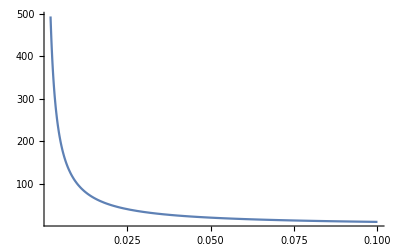

```mathematica
Plot[S[u],{u,uValues[[2]],0.1},PlotRange->All]
```

```mathematica
S[u_]:=(1/Nρofu[u]^2(1+b^3 Nρofu[u]^3(u1^2+u2^2))^(1/2))^(1/2);
Sfin[u_]:=(-1/u^3+1/u^2(1/Nρofu[u]^2(1+b^3 Nρofu[u]^3(u1^2+u2^2))^(1/2))^(1/2));
```

```mathematica
1/utest^2(1/Nρofu[utest]^2(1+b^3 Nρofu[utest]^3(u1^2+u2^2))^(1/2))^(1/2)//N
```

0.25 √((√(1.+(InverseFunction[Function[{ρ},-(ρ/(100000000000000000000 ρ (-1+Hypergeometric2F1[-1/3,1/2,2/3,-(1/1000000000000000000000000000000000000000000000000000000000000)])-Hypergeometric2F1[-1/3,1/2,2/3,-ρ^3]))]][2.])^3))/(InverseFunction[Function[{ρ},-(ρ/(100000000000000000000 ρ (-1+Hypergeometric2F1[-1/3,1/2,2/3,-1/1000000000000000000000000000000000000000000000000000000000000])-Hypergeometric2F1[-1/3,1/2,2/3,-ρ^3]))]][2.])^2)

```mathematica
utest=2
```

2

```mathematica
SJecco[[utest]] uValues[[utest]]^2+1/uValues[[utest]]//FullForm
Sfin[uValues[[utest]] ] uValues[[utest]]^2+1/uValues[[utest]]
```

493.742

493.741500787082287928241378074095825909241161859328449063633153

```mathematica
SJecco[[utest]]
Sfin[uValues[[utest]] ]
```

8.59801×10^-23

-1.5577665542661631019027967561490130127631278×10^-10

#### Inner Nodes

```mathematica
Sfin[uValues[[2]]]//Chop
```

-1.5577665542661631019027967561490130127631278×10^-10

```mathematica
uValues[[2]]
```

0.00202535131927513050548159714668361504687725757889190224777524705

```mathematica
SJecco[[2]]
```

8.59801×10^-23

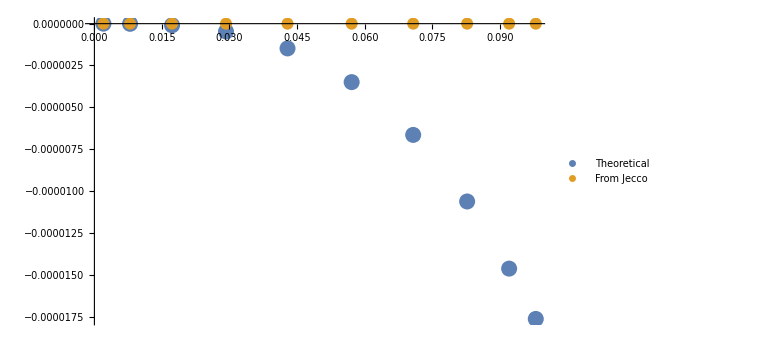

```mathematica
ListPlot[{Transpose[{uValues[[2;;uInnerNodes-1]],(Sfin/@uValues[[2;;uInnerNodes-1]])}],Transpose[{uValues[[2;;uInnerNodes-1]],SJecco[[2;;uInnerNodes-1]]}]},PlotRange->All,PlotLegends->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

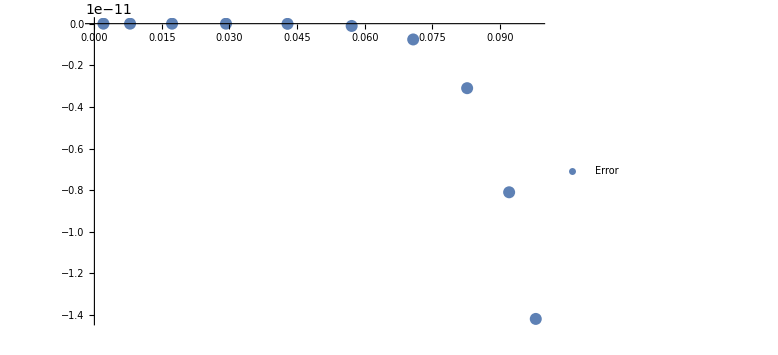

```mathematica
ListPlot[Transpose[{uValues[[2;;uInnerNodes-1]],(*(Sfin/@uValues[[2;;uInnerNodes-1]])-*)(*uValues[[2;;uInnerNodes-1]]^-1+uValues[[2;;uInnerNodes-1]]^2*)SJecco[[2;;uInnerNodes-1]]}],PlotRange->All,PlotLegends->{"Error"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

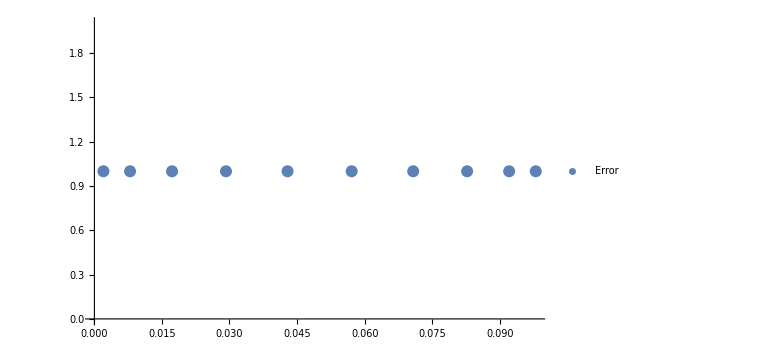

```mathematica
ListPlot[Transpose[{uValues[[2;;uInnerNodes-1]],((Sfin/@uValues[[2;;uInnerNodes-1]])-SJecco[[2;;uInnerNodes-1]])/(Sfin/@uValues[[2;;uInnerNodes-1]])}],PlotRange->All,PlotLegends->{"Error"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

#### Outer Nodes

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-1]],(S/@uValues[[uInnerNodes+1;;-1]])}],Transpose[{uValues[[uInnerNodes+1;;-1]],SJecco[[uInnerNodes+1;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.015] ,PointSize[0.0085]},ImageSize->Large]
```

-Graphics-

```mathematica
endV=-48;
```

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;endV]],(S/@uValues[[uInnerNodes+1;;endV]])-SJecco[[uInnerNodes+1;;endV]]}]},PlotRange->All,PlotLabels->{"Error"},ImageSize->Large(*,PlotLabel->Error*)]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-endV]],((S/@uValues[[uInnerNodes+1;;-endV]])-SJecco[[uInnerNodes+1;;-endV]])/(S/@uValues[[uInnerNodes+1;;-endV]])}]},PlotRange->All,PlotLabels->{"Relative Error"},ImageSize->Large(*,PlotLabel->Error*)]
```

-Graphics-

```mathematica
SJecco[[13]]//FullForm
```

9.84714

```mathematica
S[uValues[[13]]]//FullForm
```

9.84713849536516181298506082981912602951554235152569963404520544

### F function

#### From Jecco

```mathematica
FxJecco={-1.4142135623730396,-1.4142135623730496,-1.4142135623729573,-1.4142135623605776,-1.4142135620790564,-1.4142135594408454,-1.414213546006693,-1.41421350314056,-1.4142134110685944,-1.4142132753011725,-1.414213145320381,-0.1414213090835987,-0.14361664728751164,-0.15016176367897627,-0.1609347230636518,-0.17573481588432102,-0.19428627631503673,-0.21624337577327493,-0.24119677966715833,-0.2686810272731556,-0.2981829773748407,-0.32915106605125877,-0.36100525315463244,-0.3931475875223115,-0.4249733722631997,-0.4558829209859815,-0.4852938163315408,-0.5126533962728481,-0.537450932127533,-0.5592287232657304,-0.5775912465791126,-0.5922116736523471,-0.602835517374139,-0.6092817756348872,-0.6114424779396028,-0.6136024156609617,-0.6200373146872048,-0.6306127658004901,-0.645105865597385,-0.6632069098837903,-0.6845218893032525,-0.7085760776547411,-0.734819296129199,-0.7626338195868729,-0.7913462797774291,-0.8202451519856184,-0.8486052533230746,-0.8757198849981547,-0.9009396624005892,-0.9237147770563421,-0.9436348645484826,-0.9604586297577941,-0.974124925608617,-0.9847389378940123,-0.9925316879917194,-0.9977974252595044,-1.0008198929115566,-1.001802751420073,-1.002769784427095,-1.005557190307738,-1.0098226560512107,-1.014992290151557,-1.0202582649414667,-1.0245812465970945,-1.0267039642918698,-1.0251845417790477,-1.0184599975958017,-1.004950552354795,-0.9832124864865416,-0.9521395152814932,-0.9111987662865748,-0.8606682152608452,-0.8018222437476017,-0.7369999109534688,-0.6694986292943143,-0.6032732401203474,-0.5424833637617006,-0.4909968132288907,-0.45198488171729295,-0.427705239412386,-0.41947018428385685};
```

#### Analytic

```mathematica
Fx[u_]:=b^3 Nρofu[u]u1 u0d;
```

```mathematica
Fxfin[u_]:=1/u b^3 Nρofu[u]u1 u0d;
```

#### Outer Nodes

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-1]],(Fx/@uValues[[uInnerNodes+1;;-1]])}],Transpose[{uValues[[uInnerNodes+1;;-1]],FxJecco[[uInnerNodes+1;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.015] ,PointSize[0.0085]},ImageSize->Large]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-1]],(Fx/@uValues[[uInnerNodes+1;;-1]])}],Transpose[{uValues[[uInnerNodes+1;;-1]],FxJecco[[uInnerNodes+1;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.015] ,PointSize[0.0085]},ImageSize->Large]
```

-Graphics-

#### Inner Nodes

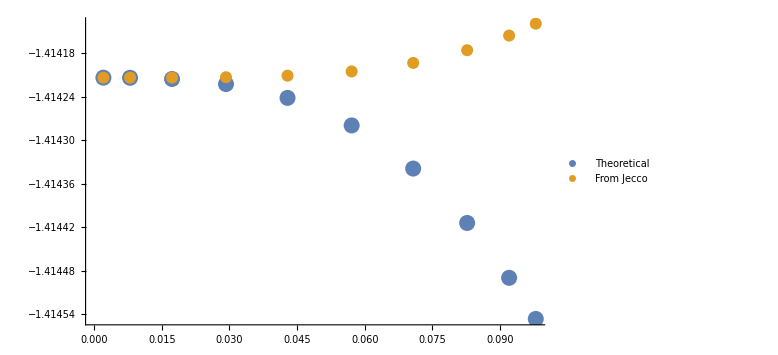

```mathematica
ListPlot[{Transpose[{uValues[[2;;uInnerNodes-1]],(Fxfin/@uValues[[2;;uInnerNodes-1]])}],Transpose[{uValues[[2;;uInnerNodes-1]],FxJecco[[2;;uInnerNodes-1]]}]},PlotRange->All,PlotLegends->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

## Inhomogeneous boosting

```mathematica
(*gdd=1/ρ^2 Table[ηdd[[u,v]]+,{u,1,4},{v,1,4}]*)
```

#### ρ

```mathematica
ClearAll[u1d,u0d,u2d]
```

```mathematica
qx=(20 Pi)/(xMax-xMin);
qy=(20 Pi)/(yMax-yMin);
(*u0d[x_,y_]=-2^(1/2);*)
u1d[x_,y_]:=Cos[qx x];
u2d[x_,y_]:=Cos[qy y];
b=1;
```

```mathematica
Solve[u1d[x,y]^2+u2d[x,y]^2-u0d[x,y]^2==-1,u0d[x,y]][[1,1,2]]
```

-√(1+Cos[2 π x]^2+Cos[2 π y]^2)

```mathematica
u0d[x_,y_]:=(*u2d[x,y]/.*)Solve[u1d[x,y]^2+u2d[x,y]^2-uu0d[x,y]^2==-1,uu0d[x,y]][[1,1,2]]
```

```mathematica
u1d[x,y]^2+u2d[x,y]^2//Simplify
```

Cos[2 π x]^2+Cos[2 π y]^2

```mathematica
u0d[x,y]
```

-√(1+Cos[2 π x]^2+Cos[2 π y]^2)

```mathematica
(*uofρ=NDSolve[{D[u[ρ],ρ]==(u[ρ]^2/ρ^2(1+(b ρ)^3(u1^2+u2^2))^(-1/2)),u[ϵ]==ϵ},u,{ρ,ϵ,1}][[1,1]];*)
```

```mathematica
(*ρofu=DSolve[{D[ρ[u,x,y],{u,1}]==(u^2/ρ[u,x,y]^2(1+(b ρ[u,x,y])^3(u1[x,y]^2+u2[x,y]^2))^(-1/2))^-1},ρ,{u,x,y}][[1,1]];*)
```

Q: Boundary conditions: at ρ=0 or =1?
A: At 0
Q: Do we know where is the horizon in the u domain?
A: Yes at u(ρ=1).

Here I compute r in function of rho. I set no boundary conditions for the ODE but I then impose the constant of integration to be zero

```mathematica
rofρ=DSolve[{D[r[ρ,x,y],{ρ}]==(-1/ρ^2(1+(b ρ)^3(u1d[x,y]^2+u2d[x,y]^2))^(-1/2))(*,r[1]==1*)},r,{ρ,x,y}][[1,1]];
rofρ=r/.rofρ
```

Function[{ρ,x,y},Hypergeometric2F1[-1/3,1/2,2/3,-1/2 ρ^3 (2+Cos[4 π x]+Cos[4 π y])]/ρ+C[1][x,y]]

#### a3

Here I compute the initial data for a3. In the limit at infinity, ρ goes to zero, as u. Anyway, they don’t have the same asymptotic behaviour so we need to take the expansion of A, substitute u to its expression that depends on  ρ, and expand in terms of ρ around infinity (where ρ=0). In this way we have an expression of our variable in terms of ρ at infinity that has to match the expression for A in the Turbulence draft (Eq. 3.7).

```mathematica
AExp=1/u^2+u a3[t,u,x,y]+(2 ξ[t,x,y])/u+ξ[t,x,y]^2-2 Derivative[1,0,0][ξ][t,x,y];
```

```mathematica
AExpOfρ=AExp/.u->rofρ[ρ,x,y]^-1(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,1}]&
```

1/ρ^2+(2 (ξ[t,x,y]+C[1][x,y]))/ρ+(ξ[t,x,y]^2+2 ξ[t,x,y] C[1][x,y]+(C[1][x,y])^2-2 ξ^(1,0,0)[t,x,y])+(a3[t,0,x,y]+1/4 (2+Cos[4 π x]+Cos[4 π y])) ρ+O[ρ]^2

```mathematica
AExpOfρ//Normal//Simplify
```

1/ρ^2+1/4 ρ (2+4 a3[t,0,x,y]+Cos[4 π x]+Cos[4 π y])+ξ[t,x,y]^2+2 ξ[t,x,y] C[1][x,y]+(C[1][x,y])^2+(2 (ξ[t,x,y]+C[1][x,y]))/ρ-2 ξ^(1,0,0)[t,x,y]

```mathematica
AToMatch=ρ^-2(1-(b ρ)^3(1+u1d[x,y]^2+u2d[x,y]^2))//Simplify
```

1/ρ^2-1/2 ρ (4+Cos[4 π x]+Cos[4 π y])

```mathematica
AExpOfρ//Normal//Simplify
```

1/ρ^2+1/4 ρ (2+4 a3[t,0,x,y]+Cos[4 π x]+Cos[4 π y])+ξ[t,x,y]^2+2 ξ[t,x,y] C[1][x,y]+(C[1][x,y])^2+(2 (ξ[t,x,y]+C[1][x,y]))/ρ-2 ξ^(1,0,0)[t,x,y]

Let' s look for ξ

```mathematica
c1Rule=Solve[Coefficient[AExpOfρ,1/ρ]==Coefficient[AToMatch,1/ρ],  C[1][x,y]]//Flatten
```

{C[1][x,y]→-ξ[t,x,y]}

Does this work with order term (it has to be checked for every configuration)???

```mathematica
SeriesCoefficient[AExpOfρ,{ρ,0,0}]/.c1Rule
```

-2 ξ^(1,0,0)[t,x,y]

xi can’t depend on t

I compare the same order coefficient of ρ

```mathematica
a3[t,0,x,y]/.Solve[Coefficient[AToMatch,ρ]==Coefficient[AExpOfρ,ρ],a3[t,0,x,y]][[1]]//Flatten//Simplify
```

1/4 (-10-3 Cos[4 π x]-3 Cos[4 π y])

#### f1 (and f2)

Same procedure as above but for F1.

```mathematica
FExp=u f1[t,z,y]+Derivative[0,1,0][ξ][t,x,y];
```

```mathematica
FExpOfρ=FExp/.u->rofρ[ρ,x,y]^-1(*/.c1Rule*)(*/.ξ->Function[{t,z,y},0]*)//Series[#,{ρ,0,1}]&
```

ξ^(0,1,0)[t,x,y]+f1[t,z,y] ρ+O[ρ]^2

```mathematica
FToMatch=(b ρ)^3/ρ^2 u0d[x,y] u1d[x,y]
```

-ρ Cos[2 π x] √(1+Cos[2 π x]^2+Cos[2 π y]^2)

```mathematica
(*f1[t,z,y]/.*)Solve[Coefficient[FToMatch,ρ]==Coefficient[FExpOfρ,ρ],f1[t,z,y]]//Flatten
```

{f1[t,z,y]→-Cos[2 π x] √(1+Cos[2 π x]^2+Cos[2 π y]^2)}

```mathematica
DSolve[SeriesCoefficient[FToMatch,{ρ,0,0}]==SeriesCoefficient[FExpOfρ,{ρ,0,0}],ξ,{t,x,y}]//Flatten
```

{ξ→Function[{t,x,y},C[1][t,y]]}

ξ can’t depend on x!

#### ξ

Does this section makes sense? The asymptotic expansion of S doesn’t say much about ξ

1/u+u^2 Sfin[t,u,z,y]+ξ[t,z,y]

```mathematica
SExp=1/u+ξ[t,x,y]+u^2 s2[t,u,x,y];
```

```mathematica
SExpOfρ=SExp/.u->rofρ[ρ,x,y]^-1/.c1Rule(*/.ξRule[[1]]*)//Series[#,{ρ,0,2}]&
```

1/ρ+(1/8 (2+Cos[4 π x]+Cos[4 π y])+s2[t,0,x,y]) ρ^2+O[ρ]^3

```mathematica
SToMatch=((1/ρ^2 √(1+ρ^3))^(1/2)//Series[#,{ρ,0,2}]&)/.√(1/ρ^2)->1/ρ//Simplify
```

1/ρ+ρ^2/4+O[ρ]^3

```mathematica
(*s0[t,0,x,y]/.*)s0Rule=Solve[Coefficient[SToMatch,ρ^2]==Coefficient[SExpOfρ,ρ^2],s2[t,0,x,y]]//Flatten
(*s0Rule[[1,1]]=ξ[t,x,y];
s0Rule*)
```

{s2[t,0,x,y]→1/8 (-Cos[4 π x]-Cos[4 π y])}

### B Function

#### Grid For ρ

The initial data for B is different, since B is defined through the entire domain. We need to invert the function r(ρ). This is a problem, since that is not invertible analytically.

```mathematica
ClearAll[uofρ]
```

```mathematica
uofρ[ρs_,xs_,ys_]:=rofρ[[2]]^-1/.c1Rule[[1]]/.ξ->Function[{t,x,y},0]/.ρ->ρs/.x->xs/.y->ys
```

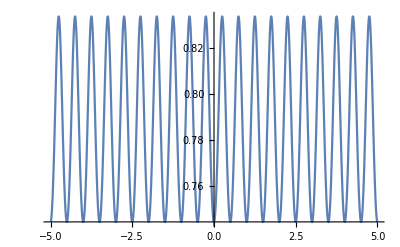

```mathematica
Plot[uofρ[1,x,1],{x,xMin,xMax}]
```

```mathematica
ContourPlot[{uofρ[1,x,y]},{x,xMin,xMax},{y,yMin,yMax},PlotLegends->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
uofρ[1,1,1]
```

1/Hypergeometric2F1[-1/3,1/2,2/3,-2]

```mathematica
ρofuOld=InverseFunction[Function[{ρ,x,y},uofρ[ρ,x,y]],1,3]
```

InverseFunction[Function[{ρ,x,y},uofρ[ρ,x,y]],1,3]

```mathematica
ρofuOld[{2,2,0.9}]//N
```

InverseFunction[Function[{ρ,x,y},uofρ[ρ,x,y]],1,3][{2.,2.,0.9}]

```mathematica
ClearAll[ρofu]
```

```mathematica
ρofu=Function[C,ρofuOld[C[[1]],C[[2]],C[[3]]]]
```

Function[C,ρofuOld[C⟦1⟧,C⟦2⟧,C⟦3⟧]]

```mathematica
ρofu[{0.9,2,0.9}]//N
```

1.61357

```mathematica
MyGrid//Dimensions
```

{59,13,13,3}

```mathematica
MyGrid[[-1,1,1]]
```

{1.1,-5,-5}

```mathematica
ρofuValues=Map[ρofu,MyGrid,{3}];//AbsoluteTiming
```

{543.804,Null}

```mathematica
ρofuValues//Dimensions
```

{59,13,13}

```mathematica
u1Values=Table[u1[xValues[[i]],yValues[[j]]],{i,1,xValues//Length},{j,1,yValues//Length}];//AbsoluteTiming
```

{0.000665,Null}

```mathematica
InitialB=Table[-1/2 Log[(1+(b ρofuValues[[ui,xi,yi]])^3 u1Values[[xi,yi]]^2)/(1+(b ρofuValues[[ui,xi,yi]])^3 u2^2)] uValues[[ui]]^-3,{ui,1,uValues//Length},{xi,1,xValues//Length},{yi,1,yValues//Length}];
InitialB[[1]]=InitialB[[2]];
```

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^3 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
ListPlot3D[InitialB[[;;,;;,1]]]
```

-Graphics3D-

```mathematica
ExportData=Join[{InitialB[[;;uInnerNodes,;;,;;]]},Table[InitialB[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1),;;,;;]],{i,0,uOuterDomains-1}]];//AbsoluteTiming
```

{0.000089,Null}

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->ExportData[[i]],{i,1,ExportAttributes//Length}];//AbsoluteTiming
```

{0.000026,Null}

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_InhomogeneusBBB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_InhomogeneusBBB.h5

```mathematica
ExpCheck=Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_InhomogeneusBBB.h5","Data"]
```

```mathematica
ListPlot3D[ExpCheck[[2]][[;;,;;,1]]]
```

-Graphics3D-

```mathematica
s0Rule
```

{ξ[t,x,y]→1/4 (1-Cos[2 π x]^2)}

### A function (for check)

#### A From Jecco

```mathematica
AJecco={-2.5,-2.500000004465527,-2.500000268782439,-2.5000027623109555,-2.5000134225856705,-2.500042392312419,-2.500100156980378,-2.500190549145636,-2.500304565096476,-2.5004195435590906,-2.5005057055958093,99.74994622655059,96.7122024669462,88.43187434940121,76.93542422354069,64.45017739493609,52.6402393099266,42.38757534163951,33.951100680417504,27.22831625744488,21.964354284370263,17.874886283486155,14.702896085112773,12.237184517233036,10.312686408589446,8.803903668325031,7.616862452729753,6.681784069613328,5.94712389377118,5.37498955593758,4.937730668253434,4.615454909884928,4.394255783818254,4.264985734960386,4.2224560544630005,4.18033311306929,4.057105802735426,3.861646748187931,3.6070729691513685,3.3087543257271816,2.982324618458698,2.6420964716614614,2.3000762714717293,1.9655759953163905,1.6452904366470416,1.3436635732197602,1.0633837960765615,0.8058919743412939,0.5718336345133503,0.36142372980503795,0.17471619375754718,0.011782811426974526,-0.127189014857127,-0.2418682313353343,-0.33180887285977206,-0.3965197305420878,-0.4355551627115424,-0.4486041625262347,-0.46163190758447453,-0.5003516679176622,-0.5637198109716819,-0.6501437605624925,-0.757672949220536,-0.8842165760410374,-1.0277556251420068,-1.186523902725671,-1.359143249191712,-1.5447076278835181,-1.7428163121030578,-1.9535560504513279,-2.1774244402273144,-2.415170118147356,-2.6674968885768964,-2.934535920766238,-3.214936620079632,-3.504394949974637,-3.793536729379919,-4.065547820476541,-4.295068777842759,-4.451228148921696,-4.506950755180788};
```

#### Analytic expression for A

```mathematica
A[u_]:=1/Nρofu[u]^2(1-b^3 Nρofu[u]^3(1+u1^2+u2^2));
Afin[u_]:=(-1/u^3+1/(u Nρofu[u]^2)(1-2 Nρofu[u]^3));
```

```mathematica
(A/@uValues)[[2]]
```

Power::infy: Infinite expression 1/0 encountered.

243780.664536102072948517054739809672724530907193429439060241634

```mathematica
uValues[[3]]//Precision
```

64.

#### Outer Nodes

```mathematica
uValues[[uInnerNodes+1]]//N
```

0.101552

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-1]],(A/@uValues[[uInnerNodes+1;;-1]])}],Transpose[{uValues[[uInnerNodes+1;;-1]],AJecco[[uInnerNodes+1;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.015] ,PointSize[0.0075]},ImageSize->Large,PlotLabel->A Function Comparison]
```

-Graphics-

```mathematica
FinalP=-1;
```

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;FinalP]],(A/@uValues[[uInnerNodes+1;;FinalP]])-AJecco[[uInnerNodes+1;;FinalP]]}]},PlotRange->All,PlotLabels->{"Error"},ImageSize->Large,PlotLabel->Absolute Error]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;FinalP]],((A/@uValues[[uInnerNodes+1;;FinalP]])-AJecco[[uInnerNodes+1;;FinalP]])/(A/@uValues[[uInnerNodes+1;;FinalP]])}]},PlotRange->All,PlotLabels->{"Error"},ImageSize->Large,PlotLabel->Relative Error]
```

-Graphics-

#### Inner Nodes

```mathematica
ListPlot[{Transpose[{uValues[[2;;uInnerNodes-1]],(Afin/@uValues[[2;;uInnerNodes-1]])}],Transpose[{uValues[[2;;uInnerNodes-1]],AJecco[[2;;uInnerNodes-1]]}]},PlotRange->All,PlotLegends->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

-Graphics-

```mathematica
ListPlot[Transpose[{uValues[[2;;uInnerNodes-1]],(Afin/@uValues[[2;;uInnerNodes-1]])-AJecco[[2;;uInnerNodes-1]]}],PlotRange->All,PlotLegends->{"Error"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

-Graphics-

```mathematica
AJecco[[3]]//FullForm
```

-2.5

### S function check

#### From Jecco

```mathematica
SJecco={0.,8.598014472498873*^-23,-2.970359103054401*^-21,-2.311669785954828*^-18,-2.654461574321596*^-16,-8.36191475146011*^-15,-1.1026791059330783*^-13,-7.59216054875459*^-13,-3.0996145403683463*^-12,-8.100666520616076*^-12,-1.4184845897796747*^-11,9.99999999999983,9.847138697790744,9.417929384269788,8.787491668396749,8.047419736242098,7.2790030125128675,6.539888335815762,5.863270418945598,5.263458174340948,4.74263165110307,4.296320092301297,3.917068886651059,3.596599583591419,3.326945537029655,3.100968049864969,2.912529264068205,2.7564908739437937,2.6286349736469923,2.5255587429197,2.4445690304738674,2.3835888667365377,2.341080648773805,2.315987211101197,2.3076905078728407,2.299453032350873,2.27523938388497,2.2364762330703307,2.1853268340647336,2.1244241882461696,2.0565862477019228,1.9845638053986885,1.91085284974246,1.8375816363214885,1.7664657840944542,1.6988153408130353,1.6355753641876942,1.5773837320456312,1.5246340816268826,1.4775361395996298,1.4361692539811872,1.4005273643869944,1.3705550509634163,1.3461749942305121,1.3273075220541792,1.3138832122187643,1.3058498846070212,1.303175664326449,1.3005115040194895,1.2926275850126256,1.279838738046411,1.2626352261077476,1.241636641674311,1.2175370141315607,1.1910478502454753,1.162844800436054,1.1335219547486957,1.1035561642324339,1.0732828893358188,1.042885281632606,1.0123995918389788,0.9817423105788645,0.9507670013099814,0.9193602209835439,0.8875837418224134,0.855860130341358,0.8251739736888752,0.7972154768074234,0.7743344496012027,0.7591530302341405,0.7538134700571201};
```

#### Analytic S

```mathematica
S[uValues[[2]]]
```

493.741500787082287928241378074095825909241161859328449063633153

```mathematica
Plot[S[u],{u,uValues[[2]],0.1},PlotRange->All]
```

-Graphics-

```mathematica
S[u_]:=(1/Nρofu[u]^2(1+b^3 Nρofu[u]^3(u1^2+u2^2))^(1/2))^(1/2);
Sfin[u_]:=(-1/u^3+1/u^2(1/Nρofu[u]^2(1+b^3 Nρofu[u]^3(u1^2+u2^2))^(1/2))^(1/2));
```

```mathematica
1/utest^2(1/Nρofu[utest]^2(1+b^3 Nρofu[utest]^3(u1^2+u2^2))^(1/2))^(1/2)//N
```

0.25 √((√(1.+(InverseFunction[Function[{ρ},-(ρ/(100000000000000000000 ρ (-1+Hypergeometric2F1[-1/3,1/2,2/3,-(1/1000000000000000000000000000000000000000000000000000000000000)])-Hypergeometric2F1[-1/3,1/2,2/3,-ρ^3]))]][2.])^3))/(InverseFunction[Function[{ρ},-(ρ/(100000000000000000000 ρ (-1+Hypergeometric2F1[-1/3,1/2,2/3,-1/1000000000000000000000000000000000000000000000000000000000000])-Hypergeometric2F1[-1/3,1/2,2/3,-ρ^3]))]][2.])^2)

```mathematica
utest=2
```

2

```mathematica
SJecco[[utest]] uValues[[utest]]^2+1/uValues[[utest]]//FullForm
Sfin[uValues[[utest]] ] uValues[[utest]]^2+1/uValues[[utest]]
```

493.742

493.741500787082287928241378074095825909241161859328449063633153

```mathematica
SJecco[[utest]]
Sfin[uValues[[utest]] ]
```

8.59801×10^-23

-1.5577665542661631019027967561490130127631278×10^-10

#### Inner Nodes

```mathematica
Sfin[uValues[[2]]]//Chop
```

-1.5577665542661631019027967561490130127631278×10^-10

```mathematica
uValues[[2]]
```

0.00202535131927513050548159714668361504687725757889190224777524705

```mathematica
SJecco[[2]]
```

8.59801×10^-23

```mathematica
ListPlot[{Transpose[{uValues[[2;;uInnerNodes-1]],(Sfin/@uValues[[2;;uInnerNodes-1]])}],Transpose[{uValues[[2;;uInnerNodes-1]],SJecco[[2;;uInnerNodes-1]]}]},PlotRange->All,PlotLegends->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

-Graphics-

```mathematica
ListPlot[Transpose[{uValues[[2;;uInnerNodes-1]],(*(Sfin/@uValues[[2;;uInnerNodes-1]])-*)(*uValues[[2;;uInnerNodes-1]]^-1+uValues[[2;;uInnerNodes-1]]^2*)SJecco[[2;;uInnerNodes-1]]}],PlotRange->All,PlotLegends->{"Error"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

-Graphics-

```mathematica
ListPlot[Transpose[{uValues[[2;;uInnerNodes-1]],((Sfin/@uValues[[2;;uInnerNodes-1]])-SJecco[[2;;uInnerNodes-1]])/(Sfin/@uValues[[2;;uInnerNodes-1]])}],PlotRange->All,PlotLegends->{"Error"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

-Graphics-

#### Outer Nodes

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-1]],(S/@uValues[[uInnerNodes+1;;-1]])}],Transpose[{uValues[[uInnerNodes+1;;-1]],SJecco[[uInnerNodes+1;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.015] ,PointSize[0.0085]},ImageSize->Large]
```

-Graphics-

```mathematica
endV=-48;
```

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;endV]],(S/@uValues[[uInnerNodes+1;;endV]])-SJecco[[uInnerNodes+1;;endV]]}]},PlotRange->All,PlotLabels->{"Error"},ImageSize->Large(*,PlotLabel->Error*)]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-endV]],((S/@uValues[[uInnerNodes+1;;-endV]])-SJecco[[uInnerNodes+1;;-endV]])/(S/@uValues[[uInnerNodes+1;;-endV]])}]},PlotRange->All,PlotLabels->{"Relative Error"},ImageSize->Large(*,PlotLabel->Error*)]
```

-Graphics-

```mathematica
SJecco[[13]]//FullForm
```

9.84714

```mathematica
S[uValues[[13]]]//FullForm
```

9.84713849536516181298506082981912602951554235152569963404520544

### F function

#### From Jecco

```mathematica
FxJecco={-1.4142135623730396,-1.4142135623730496,-1.4142135623729573,-1.4142135623605776,-1.4142135620790564,-1.4142135594408454,-1.414213546006693,-1.41421350314056,-1.4142134110685944,-1.4142132753011725,-1.414213145320381,-0.1414213090835987,-0.14361664728751164,-0.15016176367897627,-0.1609347230636518,-0.17573481588432102,-0.19428627631503673,-0.21624337577327493,-0.24119677966715833,-0.2686810272731556,-0.2981829773748407,-0.32915106605125877,-0.36100525315463244,-0.3931475875223115,-0.4249733722631997,-0.4558829209859815,-0.4852938163315408,-0.5126533962728481,-0.537450932127533,-0.5592287232657304,-0.5775912465791126,-0.5922116736523471,-0.602835517374139,-0.6092817756348872,-0.6114424779396028,-0.6136024156609617,-0.6200373146872048,-0.6306127658004901,-0.645105865597385,-0.6632069098837903,-0.6845218893032525,-0.7085760776547411,-0.734819296129199,-0.7626338195868729,-0.7913462797774291,-0.8202451519856184,-0.8486052533230746,-0.8757198849981547,-0.9009396624005892,-0.9237147770563421,-0.9436348645484826,-0.9604586297577941,-0.974124925608617,-0.9847389378940123,-0.9925316879917194,-0.9977974252595044,-1.0008198929115566,-1.001802751420073,-1.002769784427095,-1.005557190307738,-1.0098226560512107,-1.014992290151557,-1.0202582649414667,-1.0245812465970945,-1.0267039642918698,-1.0251845417790477,-1.0184599975958017,-1.004950552354795,-0.9832124864865416,-0.9521395152814932,-0.9111987662865748,-0.8606682152608452,-0.8018222437476017,-0.7369999109534688,-0.6694986292943143,-0.6032732401203474,-0.5424833637617006,-0.4909968132288907,-0.45198488171729295,-0.427705239412386,-0.41947018428385685};
```

#### Analytic

```mathematica
Fx[u_]:=b^3 Nρofu[u]u1 u0d;
```

```mathematica
Fxfin[u_]:=1/u b^3 Nρofu[u]u1 u0d;
```

#### Outer Nodes

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-1]],(Fx/@uValues[[uInnerNodes+1;;-1]])}],Transpose[{uValues[[uInnerNodes+1;;-1]],FxJecco[[uInnerNodes+1;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.015] ,PointSize[0.0085]},ImageSize->Large]
```

-Graphics-

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-1]],(Fx/@uValues[[uInnerNodes+1;;-1]])}],Transpose[{uValues[[uInnerNodes+1;;-1]],FxJecco[[uInnerNodes+1;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.015] ,PointSize[0.0085]},ImageSize->Large]
```

-Graphics-

#### Inner Nodes

```mathematica
ListPlot[{Transpose[{uValues[[2;;uInnerNodes-1]],(Fxfin/@uValues[[2;;uInnerNodes-1]])}],Transpose[{uValues[[2;;uInnerNodes-1]],FxJecco[[2;;uInnerNodes-1]]}]},PlotRange->All,PlotLegends->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.02] ,PointSize[0.015]},ImageSize->Large]
```

-Graphics-

## Black Brane

```mathematica
ExportData=Join[{uValues[[;;uInnerNodes]]},Table[uValues[[ uInnerNodes+(uOuterNodes-1) i;;uInnerNodes+(uOuterNodes-1) (i+1)]],{i,0,uOuterDomains-1}]];
```

```mathematica
ExportDataStr=Map[ToString,ExportData,{2}];
```

```mathematica
ExportAttributes=Table[ToString[i],{i,1,uOuterDomains+1}];
```

```mathematica
AttributesAndData=Table[ExportAttributes[[i]]->ExportDataStr[[i]],{i,1,ExportAttributes//Length}];
```

```mathematica
Export["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BB.h5",AttributesAndData,"Datasets"]
```

/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BB.h5

```mathematica
Import["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/InitialB_BB.h5","1"]
```

{0,0.002025351319275130505481597146683615046877257578891902247775247050,0.007937323358440941556909417554031614124335375078973105067867494116,0.01725696330273574679715374637668532234081044003315357861968521977,0.02922924934990567872353629253851883982379975447677315937868883338,0.04288425808633574297781036656918151656044743194370078357909586067,0.05711574191366425702218963343081848343955256805629921642090413933,0.07077075065009432127646370746148116017620024552322684062131116662,0.08274303669726425320284625362331467765918955996684642138031478023,0.09206267664155905844309058244596838587566462492102689493213250588,0.09797464868072486949451840285331638495312274242110809775222475295,0.1000000000000000000000000000000000000000000000000000000000000000}

```mathematica
ExportDataStr[[1]]
```

{0,0.002025351319275130505481597146683615046877257578891902247775247050,0.007937323358440941556909417554031614124335375078973105067867494116,0.01725696330273574679715374637668532234081044003315357861968521977,0.02922924934990567872353629253851883982379975447677315937868883338,0.04288425808633574297781036656918151656044743194370078357909586067,0.05711574191366425702218963343081848343955256805629921642090413933,0.07077075065009432127646370746148116017620024552322684062131116662,0.08274303669726425320284625362331467765918955996684642138031478023,0.09206267664155905844309058244596838587566462492102689493213250588,0.09797464868072486949451840285331638495312274242110809775222475295,0.1000000000000000000000000000000000000000000000000000000000000000}

### S function

#### From Jecco

```mathematica
SBBJecco={0.,-7.767073443078426*^-43,8.868457768027458*^-42,-4.650050025528685*^-41,-9.79745026741803*^-41,-2.478312070370561*^-40,-5.640346544054392*^-40,-1.260302885079073*^-39,-2.8765023141569715*^-39,-3.867537313122834*^-39,-4.3238212364208625*^-39,10.,9.847138697790948,9.417929384270114,8.787491668397436,8.047419736243924,7.279003012518429,6.539888335833936,5.863270419006205,5.263458174539939,4.742631651730042,4.296320094163855,3.9170688918086607,3.596599596811057,3.3269455682694424,3.100968117796434,2.9125293999058273,2.756491123747342,2.628635396344959,2.5255594015143936,2.444569976016672,2.3835901184697508,2.341082177581642,2.3159889344941833,2.3076923014325454,2.2994548986768177,2.275241483452247,2.236478775143221,2.1853301233592415,2.124428696091271,2.056592724083866,1.9845734543797156,1.9108675966336468,1.8376045169006887,1.7665014773303631,1.6988708373599068,1.6356607034687487,1.5775126473256276,1.5248242775813505,1.4778088292185692,1.436547567764204,1.4010333919242703,1.371205629486919,1.346976880402942,1.3282531083991505,1.3149482171008207,1.3069942099840324,1.3043478154723833,1.301712116114504,1.2939169564947643,1.2812877830157992,1.2643342217286977,1.2437066496375944,1.2201453560666387,1.194429247793589,1.167329934411575,1.1395750711070751,1.1118226688637676,1.0846462163316364,1.058529169401708,1.0338667025460433,1.01097247484889,0.990088371998002,0.9713955737726898,0.9550257334893321,0.9410714583359033,0.9295956065024944,0.9206391572086828,0.9142275693146376,0.9103756373616126,0.9090908967608278};
```

#### Analytical

```mathematica
SBB[u_]:=1/u
```

#### Comparison

```mathematica
ListPlot[{Transpose[{uValues[[uInnerNodes+1;;-1]],(SBB/@uValues[[uInnerNodes+1;;-1]])}],Transpose[{uValues[[uInnerNodes+1;;-1]],SBBJecco[[uInnerNodes+1;;-1]]}]},PlotRange->All,PlotLabels->{"Theoretical","From Jecco"}, 
 PlotStyle -> {PointSize[0.015] ,PointSize[0.0085]},ImageSize->Large]
```

-Graphics-

## Benchmark

```mathematica
ClearAll[u2]
```

Solve for θ

```mathematica
Solve[{Σ^2 Sinh[t]==b^3 rho u1 u2},t]
```

{{t→ConditionalExpression[ⅈ π-ArcSinh[(b^3 rho u1 u2)/Σ^2]+2 ⅈ π C[1], C[1]∈ℤ]},{t→ConditionalExpression[ArcSinh[(b^3 rho u1 u2)/Σ^2]+2 ⅈ π C[1], C[1]∈ℤ]}}

Solve for Σ

```mathematica
Σ^4 Cosh[t]^2==1/rho^4(1+(b rho)^3 u1^2)(1+(b rho)^3 u2^2)/.t->ArcSinh[(b^3 rho u1 u2)/Σ^2]
```

(1+(b^6 rho^2 u1^2 u2^2)/Σ^4) Σ^4==((1+b^3 rho^3 u1^2) (1+b^3 rho^3 u2^2))/rho^4

```mathematica
Σ^4(1+((b^3 rho u1 u2)/Σ^2)^2)==1/rho^4(1+(b rho)^3 u1^2)(1+(b rho)^3 u2^2)//Simplify
```

```mathematica
1/rho+b^3 rho^2 (u1^2+u2^2)==rho^3 Σ^4//Solve[#,Σ]&
```

{{Σ→-((1+b^3 rho^3 u1^2+b^3 rho^3 u2^2)^(1/4))/rho},{Σ→-(ⅈ (1+b^3 rho^3 u1^2+b^3 rho^3 u2^2)^(1/4))/rho},{Σ→(ⅈ (1+b^3 rho^3 u1^2+b^3 rho^3 u2^2)^(1/4))/rho},{Σ→((1+b^3 rho^3 u1^2+b^3 rho^3 u2^2)^(1/4))/rho}}

And Sinhθ

```mathematica
(b^3 rho u1 u2)/Σ^2/.Σ->((1+b^3 rho^3 u1^2+b^3 rho^3 u2^2)^(1/4))/rho
```

(b^3 rho^3 u1 u2)/(√(1+b^3 rho^3 u1^2+b^3 rho^3 u2^2))